```mathematica
$Assumptions=t>=0&&n>1&&n∈Integers&&Subscript[λ, _]>0&&sumλ>0&&Δ>0&&t1>=0&&t2>=0
```

t≥0&&n>1&&n∈ℤ&&λ__>0&&sumλ>0&&Δ>0&&t1≥0&&t2≥0

```mathematica
t≥0&&n>1&&n∈Integers&&Subscript[λ, _]>0&&sumλ>0&&Δ>0&&t1≥0&&t2≥0
```

```mathematica
p[i_,t_]:=PDF[𝒟t[Subscript[λ, i]],t]
p1[t_,n_]:=∑_(i=1)^n (p[i,t](∏_(j=1)^n SurvivalFunction[𝒟t[Subscript[λ, j]],t])/SurvivalFunction[𝒟t[Subscript[λ, i]],t])
```

```mathematica
𝒟t=ExponentialDistribution
```

```mathematica
FullSimplify[p1[t,n]]/.{∑_(i=1)^n (∏_(j=1)^n ⅇ^(-t Subscript[λ, j])) Subscript[λ, i]->(ⅇ^(-t ∑_(i=1)^n Subscript[λ, i]))∑_(i=1)^n Subscript[λ, i]}/.{∑_(i=1)^n Subscript[λ, i]->sumλ}
```

```mathematica
pFirst[t_]:=ⅇ^(-t sumλ) sumλ
```

```mathematica
FullSimplify[∫_0^∞ (τ×pFirst[τ])ⅆτ]
```

```mathematica
p12[t1_,t2_]:=∑_(i=1)^n (∑_(j=1)^n (p[i,t1]p[j,t2](∏_(k=1)^n SurvivalFunction[𝒟t[Subscript[λ, k]],t2])/(SurvivalFunction[𝒟t[Subscript[λ, i]],t2]SurvivalFunction[𝒟t[Subscript[λ, j]],t2])×HeavisideTheta[t2-t1])×Boole[i≠j])
```

```mathematica
FullSimplify[p12[t1,t2]]
```

```mathematica
FullSimplify[∫_0^∞ ∫_0^∞ (DiracDelta[Δ-t2+t1]×p12[t1,t2])ⅆt2ⅆt1]
```

```mathematica
FullSimplify[ExpandAll[ⅇ^(-t1 Subscript[λ, i]+(t1+Δ) Subscript[λ, i]) (∏_(k=1)^n ⅇ^(-((t1+Δ) Subscript[λ, k]))) Subscript[λ, i] Subscript[λ, j]]/.{∏_(k=1)^n ⅇ^(-((t1+Δ) Subscript[λ, k]))->ⅇ^(-(t1+Δ)∑_(k=1)^n Subscript[λ, k])}/.{∑_(k=1)^n Subscript[λ, k]->sumλ}]
```

```mathematica
integrand[i_,j_,t1_]:=ⅇ^(-((t1+Δ) sumλ)+Δ Subscript[λ, i]) Subscript[λ, i] Subscript[λ, j]
```

```mathematica
FullSimplify[ExpandAll[Integrate[∑_(i=1)^n ((∑_(j=1)^n integrand[i,j,t1])-integrand[i,i,t1]),{t1,0,∞}]]]
```

```mathematica
FullSimplify[ExpandAll[∑_(i=1)^n ⅇ^(-Δ(sumλ-Subscript[λ, i]))∫_0^∞ ⅇ^(-t1 sumλ) Subscript[λ, i](-Subscript[λ, i]+∑_(j=1)^n Subscript[λ, j])ⅆt1]]
```

```mathematica
(∑_(i=1)^n ⅇ^(-Δ (sumλ-Subscript[λ, i])) Subscript[λ, i] (-Subscript[λ, i]+∑_(j=1)^n Subscript[λ, j]))/sumλ/.{∑_(j=1)^n Subscript[λ, j]->sumλ}
```

```mathematica
(∑_(i=1)^n ⅇ^(-Δ (sumλ-Subscript[λ, i])) (sumλ-Subscript[λ, i]) Subscript[λ, i])/sumλ/.{sumλ->∑_(j=1)^n Subscript[λ, j]}
```

```mathematica
pDeltaConditional[Δ_,n_]:=(∑_(i=1)^n ⅇ^(-Δ (-Subscript[λ, i]+∑_(j=1)^n Subscript[λ, j])) Subscript[λ, i] (-Subscript[λ, i]+∑_(j=1)^n Subscript[λ, j]))/(∑_(j=1)^n Subscript[λ, j])
```

```mathematica
joint𝒟[sumλ_,n_]:=ProductDistribution[{𝒟[sumλ,n],n}]
Λ[n_]:=Array[Subscript[λ, #]&,{n}]
limits[n_]:=Table[{Subscript[λ, i],0,∞},{i,1,n}]
```

```mathematica
pDelta1[Δ_,sumλ_,n_]:=NIntegrate[pDeltaConditional[sumλ,n]×PDF[joint𝒟[sumλ,n],Λ[n]],Evaluate[Sequence@@limits[n]]]
```

```mathematica
Az[x_,sumλ_,n_]:=NIntegrate[λ×ⅇ^(-x×λ)×PDF[𝒟[sumλ,n],λ],{λ,0,∞}]
Bz[x_,Δ_,sumλ_,n_]:=NIntegrate[λ×ⅇ^(-λ×(x+Δ))×PDF[𝒟[sumλ,n],λ],{λ,0,∞}]
Cz[x_,Δ_,sumλ_,n_]:=NIntegrate[ⅇ^(-λ×(x+Δ))×PDF[𝒟[sumλ,n],λ],{λ,0,∞}]
```

```mathematica
pDeltaIntegrand[x_,Δ_,sumλ_,n_]:=Az[x,sumλ,n]×Bz[x,Δ,sumλ,n]×(Cz[x,Δ,sumλ,n])^(n-2)
```

```mathematica
pDelta2[Δ_,sumλ_,n_]:=n×(n-1)×NIntegrate[pDeltaIntegrand[x,Δ,sumλ,n],{x,0,∞}]
```

```mathematica
pDelta[Δ_,sumλ_,n_]:=pDelta2[Δ,sumλ,n]
```

```mathematica
forkRate[propTime_,sumλ_,n_]:=NIntegrate[pDelta[Δ,sumλ,n],{Δ,0,propTime}]
```

```mathematica
lomax[sumλ_,n_,α_]:=ParetoDistribution[((α-1)sumλ)/n,α,0]
(*lomax2[sumλ_,n_,α_]:=BetaPrimeDistribution[1,α,1,((α-1)sumλ)/n]*)
```

```mathematica
sumλValue=1/600
```

1/600

```mathematica
α=1.3
```

1.3

```mathematica
(*PDF[lomax[sumλValue,3,α],4]/PDF[lomax2[sumλValue,3,α],4]*)
```

```mathematica
𝒟[sumλ_,n_]:=lomax[sumλ,n,α]
```

```mathematica
FullSimplify[ExpandAll[λ×ⅇ^(-x×λ)×PDF[𝒟[sumλ,n],λ]]]
```

```mathematica
pDelta[Δ_,sumλ_,n_]:=pDelta2[Δ,sumλ,n]
```

```mathematica
LaunchKernels[];
ParallelTable[forkRate[8.7,sumλValue,n],{n,2,30}]
```

{0.00193697,0.00310371,0.00391529,0.00452683,0.00501168,0.00540989,0.00574554,0.00603413,0.00628617,0.00650913,0.00670843,0.00688818,0.00705153,0.00720093,0.00733837,0.00746543,0.00758342,0.00769342,0.00779634,0.00789295,0.00798388,0.00806972,0.00815093,0.00822794,0.00830112,0.0083708,0.00843725,0.00850073,0.00856147}

```mathematica
pDelta[Δ_,sumλ_,n_]:=pDelta1[Δ,sumλ,n]
```

```mathematica
forkRate[8.7,sumλValue,3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.00313051

```mathematica
logNormalD[sumλ_,n_,σ_]:=LogNormalDistribution[Log[sumλ/n]-σ^2/2,σ]
```

```mathematica
σ=1.11
```

1.11

```mathematica
𝒟[sumλ_,n_]:=logNormalD[sumλ,n,σ]
```

```mathematica
LaunchKernels[];
ParallelTable[forkRate[8.7,sumλValue,n],{n,2,30}]
```

{0.00428444,0.00644238,0.0077818,0.00870703,0.00938988,0.00991722,0.0103382,0.0106829,0.0109709,0.0112154,0.0114259,0.0116091,0.0117702,0.0119129,0.0120404,0.012155,0.0122586,0.0123528,0.0124388,0.0125176,0.0125901,0.0126571,0.0127192,0.0127768,0.0128306,0.0128808,0.0129278,0.0129719,0.0130134}

```mathematica
pDelta[Δ_,sumλ_,n_]:=pDelta2[Δ,sumλ,n]
```

```mathematica
Table[forkRate[8.7,sumλValue,n],{n,2,9}]
```

```mathematica
(*Exponential*)
```

```mathematica
𝒟[sumλ_,n_]:=ExponentialDistribution[n/sumλ]
```

```mathematica
Az[x_,sumλ_,n_]:=(n sumλ)/(n+sumλ x)^2
```

```mathematica
Bz[x_,Δ_,sumλ_,n_]:=(n sumλ)/(n+sumλ x+sumλ Δ)^2
```

```mathematica
Cz[x_,Δ_,sumλ_,n_]:=n/(n+sumλ x+sumλ Δ)
```

```mathematica
FullSimplify[ExpandAll[Az[x,sumλ,n]×Bz[x,Δ,sumλ,n]×(Cz[x,Δ,sumλ,n])^(n-2)]]
```

```mathematica
pDeltaIntegrand[x_,Δ_,sumλ_,n_]:=(sumλ^2 (n/(n+sumλ (x+Δ)))^n)/(n+sumλ x)^2
```

```mathematica
N[pDeltaIntegrand[11550,3,sumλValue,4]]
```

4.49807×10^-12

```mathematica
NIntegrate[pDeltaIntegrand[x,3,sumλValue,4],{x,0,∞}]
```

0.000082987

```mathematica
FullSimplify[ExpandAll[1/((n/sum_lambda+x)^2*(n/sum_lambda+x+delta)^n)*(n/sum_lambda)^n]]
```

(n^n sum_lambda^2 (n+(delta+x) sum_lambda)^-n)/(n+x sum_lambda)^2

```mathematica
pDelta2[Δ_,sumλ_,n_]:=n×(n-1)×NIntegrate[pDeltaIntegrand[x,Δ,sumλ,n],{x,0,∞}]
```

```mathematica
pDelta[Δ_,sumλ_,n_]:=pDelta2[Δ,sumλ,n]
```

```mathematica
LaunchKernels[];
ParallelTable[forkRate[0.87,sumλValue,n],{n,2,30}]
```

{0.000483071,0.00072458,0.000869475,0.000966066,0.00103506,0.0010868,0.00112704,0.00115924,0.00118558,0.00120753,0.0012261,0.00124202,0.00125581,0.00126788,0.00127854,0.001288,0.00129648,0.0013041,0.001311,0.00131727,0.00132299,0.00132824,0.00133307,0.00133753,0.00134165,0.00134549,0.00134905,0.00135238,0.0013555}

```mathematica
LaunchKernels[];
ParallelTable[forkRate[8.7,sumλValue,n],{n,2,30}]
```

{0.0048072,0.00720817,0.00864771,0.0096069,0.0102918,0.0108053,0.0112046,0.0115239,0.0117852,0.0120029,0.012187,0.0123449,0.0124817,0.0126013,0.0127069,0.0128008,0.0128848,0.0129603,0.0130287,0.0130908,0.0131476,0.0131996,0.0132475,0.0132916,0.0133325,0.0133705,0.0134058,0.0134388,0.0134697}

```mathematica
λ[n_] :=Table[RandomVariate[logNormalD[sumλValue,n,σ]],{i,1,n}]
ts[n_]:=RandomVariate[ExponentialDistribution[#]]&/@λ[n]
tmin[n_]:=Min[ts[n]]
ts[19]
```

```mathematica
Mean@Table[tmin[50],{1000000}]
```

1.

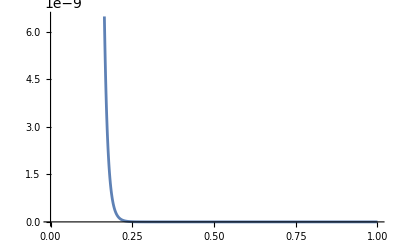

```mathematica
probdelay[delta_,mu_,Nminers_]:=((Nminers-1) mu^(Nminers-1)/(mu+delta)^Nminers);

NIntegrate[probdelay[y,0.1,25],{y,0.,Infinity}]

Plot[probdelay[delta,0.1,25],{delta,0.,1},PlotRange->Automatic]
```